ⅇ

Log[x]/Log[10]

ⅇ^(x (-0.0000111111 per meter)) (12.5 mg/L)

0.3 per day

0.18 per day

12.5 mg/L

0.5 m/s

0 km

60 km

1 mg/L

C:\Users\xy790\Desktop

./1.txt

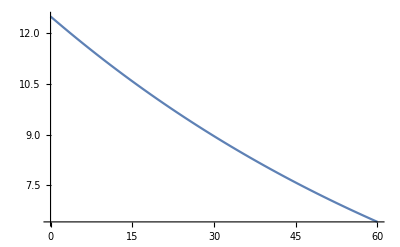

{{1.22449×10^-6,12.5},{0.0184031,12.4974},{0.0368049,12.4949},{0.0736086,12.4898},{0.147216,12.4796},{0.294431,12.4592},{0.58886,12.4185},{1.17772,12.3375},{2.4545,12.1637},{3.64667,12.0036},{4.81546,11.8488},{6.08331,11.683},{7.26655,11.5304},{8.54885,11.3673},{9.80777,11.2094},{10.9821,11.0641},{12.2554,10.9087},{13.4442,10.7655},{14.6096,10.627},{15.874,10.4788},{17.0538,10.3423},{18.3327,10.1964},{19.5882,10.0551},{20.7591,9.92515},{22.0291,9.78608},{23.2144,9.65804},{24.4988,9.52118},{25.7599,9.38871},{26.9363,9.26679},{28.2118,9.13638},{29.4026,9.01629},{30.5701,8.90008},{31.8367,8.77571},{33.0186,8.66122},{34.2996,8.53881},{35.5572,8.42033},{36.7302,8.31129},{38.0023,8.19465},{39.1897,8.08724},{40.3538,7.98331},{41.6169,7.87205},{42.7955,7.76964},{44.0731,7.66012},{45.266,7.55926},{46.4356,7.46166},{47.7043,7.35721},{48.8883,7.26105},{50.1714,7.15827},{51.4312,7.05877},{52.6063,6.96721},{53.8804,6.86926},{55.07,6.77907},{56.2362,6.6918},{57.5014,6.59838},{58.6821,6.51239},{58.7027,6.5109},{58.7232,6.50941},{58.7644,6.50643},{58.8468,6.50048},{59.0115,6.48859},{59.341,6.46488},{59.3616,6.4634},{59.3822,6.46192},{59.4234,6.45896},{59.5058,6.45305},{59.6705,6.44125},{59.6911,6.43978},{59.7117,6.43831},{59.7529,6.43536},{59.8353,6.42947},{59.8558,6.428},{59.8764,6.42653},{59.9176,6.42359},{59.9382,6.42212},{59.9588,6.42065},{59.9794,6.41918},{60.,6.41771}}

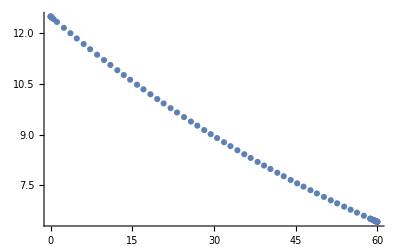

./1.txt

```mathematica
(*This is a dual function ploting program*)
Clear["Global`*"]
(*Preparpration*)
e=Exp[1]
(*lg支持LaTex格式，且需要加括号*)
lg[x_]=Log10[x]
QPlot[fn_,intvl_,options___]:=Module[{func,externalSymbol,localVar,minQ,maxQ,unit},externalSymbol=Unevaluated[intvl]/.{x_,y__}:>HoldPattern[x];
{minQ,maxQ}=Rest[intvl];
unit=QuantityUnit[minQ];
func=Unevaluated[fn]/.externalSymbol:>Unevaluated[Quantity[localVar,unit]];
Plot[func,{localVar,QuantityMagnitude[minQ,unit],QuantityMagnitude[maxQ,unit]},options]];



(*---------------------------------------------*)
(*Part1-Variable definitions*)
(*两个自定义函数*)
function1=Subscript[ρ, BO Subscript[D, 0]] e^(−(Subscript[k, 1]+Subscript[k, 3])x/Subscript[u, x])
(*方程各参数*)
Subscript[k, 1]=Quantity[0.3, 1/("Days")]
Subscript[k, 3]=Quantity[0.18, 1/("Days")]
Subscript[ρ, BO Subscript[D, 0]]=Quantity[12.5, ("Milligrams")/("Liters")]
Subscript[u, x]=Quantity[0.5, ("Meters")/("Seconds")]


(*绘图设置*)
(*x轴坐标范围*)
plotrangMin=Quantity[0, "Kilometers"]
plotrangMax=Quantity[60, "Kilometers"]
(*y轴的单位*)
yunit=Quantity[, ("Milligrams")/("Liters")]




(*数据存储位置*)
SetDirectory[NotebookDirectory[]]
Exportdir1="./1.txt"

(*---------------------------------------------*)



(*The default way is smart picking depended on "Plot"*)
plot1=QPlot[UnitConvert[function1,yunit],{x,plotrangMin,plotrangMax}]
data1=InputForm[plot1][[1,1,1,1,3,1,2,1]]
ListPlot[data1]
Export[Exportdir1,data1,"Table"]
(*This is another way "Table" to pick points, evently*)
(*data1=Table[{x,function1},{x,plotrangMin,plotrangMax,plotstep}]
ListPlot[data1]
*)
(*lg支持LaTex格式，且需要加括号*)
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["./1.txt"]]]
```